### Categorization

Tutorial

MeshTools Package

MeshTools`

MeshTools/tutorial/StructuredMeshGeneration

### Keywords

Details

# Structured Mesh Generation

This tutorial describes procedures to create nice structured ElementMesh objects in 2D and 3D.

This loads the package:

```mathematica
Needs["MeshTools`"]
```

## Create structured mesh of layered cylinder

DiskMesh[{x,y},r,n] | creates structured mesh with n elements on Disk of radius r centered at {x,y}.
AnnulusMesh[{x,y},{rIn,rOut},{ϕ1,ϕ2},{nϕ,nr}] | creates mesh on Annulus with nϕ elements in circumferential and nr elements in radial direction.
ExtrudeMesh[mesh, thickness, layers] | extrudes 2D quadrilateral mesh to 3D hexahedron mesh.

Main function to create structured mesh on cylinder.

Define position and dimensions of cylinder together with number of elements.

```mathematica
center={0,0};
r1=0.9; (* inner radius *)
r2=1.; (* outer radius *)
n1=10; (* number of elements on quarter of disk perimeter *)
length=3; (* length of cylinder *)
n2=10; (* number of elements in length direction *)
```

First create mesh on disk and annulus with matching element spacing.

```mathematica
diskMesh=DiskMesh[center,r1,n1]
```

ElementMesh[{{-0.9,0.9},{-0.9,0.9}},{QuadElement[<500>]}]

```mathematica
annulusMesh=AnnulusMesh[center,{r1,r2},{0,2Pi},{4*n1,3}]
```

ElementMesh[{{-1.,1.},{-1.,1.}},{QuadElement[<120>]}]

Visualise these two separate 2D meshes together to see if their edges match.

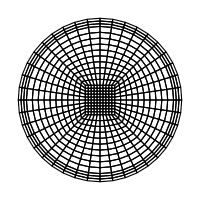

```mathematica
Show[
diskMesh["Wireframe"],
annulusMesh["Wireframe"],
ImageSize->200
]
```

Disk and annulus meshes are extruded in the third dimension and distinct markers are added to each mesh. Then meshes are merged into one 3D mesh and element markers are preserved.

```mathematica
mesh3D=MergeMesh@{
AddMeshMarkers[ExtrudeMesh[diskMesh,length,n2],1],
AddMeshMarkers[ExtrudeMesh[annulusMesh,length,n2],2]
}
```

ElementMesh[{{-1.,1.},{-1.,1.},{0.,3.}},{HexahedronElement[<6200>]}]

```mathematica
mesh3D["Wireframe"[
"MeshElement"->"MeshElements",
ImageSize->400,
Axes->True,
"MeshElementStyle"->{FaceForm[Green],FaceForm[Orange]},
Lighting->{{"Ambient", White}}
]]
```

-Graphics3D-

More About

Related Tutorials

Element Mesh Generation

Related Wolfram Education Group Courses